# Deuteron content of the final 3-body state 15/08/24

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
```

[σ_tot]=μb=10^-4 fm^2
[σ_tot]=mb=10^-1 fm^2
[Lab photon energy] = MeV

```mathematica
dbg=False;
```

#### set of regulator functions to smooth the discrete result of the inverse Lorentz transform

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy,LinearSolve::luc]
Needs["MaTeX`"]
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts}"}];

readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];

trafoToIHeNorm[normMat_]:=Block[{dbg=True},
{evaln,evecn}=Eigensystem[normMat];

diagev=DiagonalMatrix[evaln^(-0.5)];
fulltrafo=Transpose[evecn].diagev;
fulltrafo
];
trafoToIHeNormStab[normMat_,cutoff_:0.0]:=Block[{dbg=True},
{evaln,evecn}=Transpose[Select[Sort[Transpose[Eigensystem[normMat]],#1[[1]]<#2[[1]]&],#[[1]]>cutoff&]];
diagev=DiagonalMatrix[evaln^(-0.5)];
fulltrafo=Transpose[evecn].diagev;
fulltrafo
];
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={0.5}; (*Spin of Excited states*)
J0=0.5; (*Spin of Ground states which consists of two channels s and d*)
mIns=Range[-#,#,1]&/@Subscript[I, n];
lege="J_lit="<>ToString[#]&/@Subscript[I, n];
EVthreshold=(10.)^(-8);
dH=1; (* this takes only every dH basis vector into account; ECCE: not benchmarked *)
```

```mathematica
ImgSize=900;
mnucl=938.3;
hbarc=197.3269804; (*codata*)

hbarsqO2m=hbarc^2/(2 mnucl);
(*αfine=1./137.*)
αfine=UnitConvert[Quantity[1,"FineStructureConstant"]];
hat[l_]:=Sqrt[2 l+1];

resultsDir2="/home/kirscher/kette_repo/IRS/Projection";
resultsDir="/home/kirscher/kette_repo/IRS/Projection/3body";

files=FileNames[All,resultsDir];
anzBas=Length[Select[files,StringMatchQ[#,"*mat*BasNR*"]&]]/Length[Subscript[I, n]];

SetDirectory[resultsDir];
dt=ToString[Import["dtype.dat"][[1]][[1]]];
datatype="Real64";
Which[dt=="float32",datatype="Real32",dt=="float64",datatype="Real64"];
Print["Read FORTRAN results from \n",Style[resultsDir,18,Red],"\nin\n",Style[dt,18,Red],"=",Style[datatype,18,Red],"\nformat for\nN_bases=",Style[anzBas,18,Red],"\nevolved bases for the expansion of the final state."];
```

Read FORTRAN results from 
/home/kirscher/kette_repo/IRS/Projection/3body
in
float64=Real64
format for
N_bases=2
evolved bases for the expansion of the final state.

### Read H_αβ^J:=⟨α|(Ĥ)_(V18+UIX)|β⟩ and 𝕟_αβ^J:=⟨α|OverHat[𝟙]|β⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the final state, i.e., J^π=(0)^- or J^π=(1)^- or J^π=(2)^- for the negative-parity rank-1 E_1 operator perturbing a Helion;

```mathematica
matnames=FileNames["mat_*^-_BasNR-*"];
matnamesJ=Table[Select[matnames,StringMatchQ[#,"*"<>ToString[Subscript[I, n][[Inn]]]<>"*"]&],{Inn,Range[Length[Subscript[I, n]]]}];

FSNormHamMat=Table[readREAL8list[#]&/@Sort[matnamesJ[[Inn]],ToExpression[StringSplit[#1,"-"][[-1]]]<ToExpression[StringSplit[#2,"-"][[-1]]]&],{Inn,Range[Length[Subscript[I, n]]]}];

FSbasisDim=Table[IntegerPart[Sqrt[Length[#] 0.5]]&/@FSNormHamMat[[Inn]],{Inn,Range[Length[Subscript[I, n]]]}];

Print["Final-state-basis Dimension = ",FSbasisDim];
FSNormBare=Table[ArrayReshape[FSNormHamMat[[Inn]][[#]][[1;;FSbasisDim[[Inn]][[#]]^2]],{FSbasisDim[[Inn]][[#]],FSbasisDim[[Inn]][[#]]}][[;;;;dH,;;;;dH]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
FSHamBare=Table[ArrayReshape[FSNormHamMat[[Inn]][[#]][[FSbasisDim[[Inn]][[#]]^2+1;;]],{FSbasisDim[[Inn]][[#]],FSbasisDim[[Inn]][[#]]}][[;;;;dH,;;;;dH]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
```

Final-state-basis Dimension = {{324,324}}

transform this basis s.t. one can safely “insert 𝟙”:

```mathematica
fulltrafosαβ=Table[trafoToIHeNormStab[FSNormBare[[Inn]][[#]],EVthreshold]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
fulltrafosαβInstab=Table[trafoToIHeNorm[FSNormBare[[Inn]][[#]]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
Print["threshold-less reordering and diagonal-normalizing basis trafo: ",Dimensions[fulltrafosαβInstab[[1]][[1]]]];
Print[EVthreshold," threshold for norm eigenvalues: ",Dimensions[fulltrafosαβ[[1]][[1]]]];
Table[Select[ArrayRules[SparseArray[Chop[Transpose[fulltrafosαβ[[nj]][[nb]]].FSNormBare[[nj]][[nb]].fulltrafosαβ[[nj]][[nb]]]]],#[[1]][[1]]!=#[[1]][[2]]&],{nj,Range[Length[Subscript[I, n]]]},{nb,Range[anzBas]}];
FSHam=Table[Transpose[fulltrafosαβ[[nj]][[nb]]].FSHamBare[[nj]][[nb]].fulltrafosαβ[[nj]][[nb]],{nj,Range[Length[Subscript[I, n]]]},{nb,Range[anzBas]}];
FSNorm=Table[Transpose[fulltrafosαβ[[nj]][[nb]]].FSNormBare[[nj]][[nb]].fulltrafosαβ[[nj]][[nb]],{nj,Range[Length[Subscript[I, n]]]},{nb,Range[anzBas]}];
FSHamInstab=Table[Transpose[fulltrafosαβInstab[[nj]][[nb]]].FSHamBare[[nj]][[nb]].fulltrafosαβInstab[[nj]][[nb]],{nj,Range[Length[Subscript[I, n]]]},{nb,Range[anzBas]}];
FSNormInstab=Table[Transpose[fulltrafosαβInstab[[nj]][[nb]]].FSNormBare[[nj]][[nb]].fulltrafosαβInstab[[nj]][[nb]],{nj,Range[Length[Subscript[I, n]]]},{nb,Range[anzBas]}];
Print["bare/stabilized final-state dimension: ",Dimensions[FSHamBare[[1]][[1]]],"/",Dimensions[FSHam[[1]][[1]]]];
FSNormBare[[1]][[1]][[;;5,;;5]]//MatrixForm
FSNormInstab[[1]][[1]][[;;5,;;5]]//MatrixForm
FSNorm[[1]][[1]][[;;5,;;5]]//MatrixForm
```

threshold-less reordering and diagonal-normalizing basis trafo: {324,324}

1.×10^-8 threshold for norm eigenvalues: {324,324}

bare/stabilized final-state dimension: {324,324}/{324,324}

(1. | 0.179407 | 0.00391825 | 0.00115085 | 0.000410494
0.179407 | 1. | 0.0944365 | 0.0293874 | 0.0106912
0.00391825 | 0.0944365 | 1. | 0.747503 | 0.403184
0.00115085 | 0.0293874 | 0.747503 | 1. | 0.812705
0.000410494 | 0.0106912 | 0.403184 | 0.812705 | 1.)

(1. | 2.44258×10^-33 | -7.70372×10^-33 | -2.22045×10^-16 | 1.31926×10^-32
1.10818×10^-32 | 1. | 9.27847×10^-33 | 1.06195×10^-33 | -1.29975×10^-34
-5.3926×10^-33 | 8.76211×10^-34 | 1. | 4.81482×10^-33 | -4.85723×10^-17
1.66533×10^-16 | -9.25324×10^-33 | -1.54074×10^-33 | 1. | 8.47409×10^-33
1.25908×10^-32 | 1.92895×10^-33 | 2.94903×10^-17 | 1.12667×10^-32 | 1.)

(1. | -9.60978×10^-10 | 1.44096×10^-10 | 2.25519×10^-11 | -1.73228×10^-10
-7.88302×10^-10 | 1. | -1.03583×10^-9 | 1.69215×10^-10 | -2.005×10^-10
3.78359×10^-9 | -8.41922×10^-10 | 1. | -1.32353×10^-10 | 1.61962×10^-11
-6.52981×10^-10 | -1.67736×10^-10 | -4.52161×10^-10 | 1. | 2.34977×10^-10
-3.20448×10^-10 | 7.65714×10^-11 | 1.64635×10^-10 | -4.88039×10^-10 | 1.)

#### The final states

for the projection calculation, I initially chose no stabilizing elimination of small norm ev and no reordering of the basis

```mathematica
esysFSp=Table[Sort[Transpose[Eigensystem[{FSHamBare[[Inn]][[Nbb]],FSNormBare[[Inn]][[Nbb]]}]],Re[#1[[1]]]<Re[#2[[1]]]&],{Inn,Range[1,Length[Subscript[I, n]]]},{Nbb,Range[anzBas]}];
esysFSp[[1]][[1]][[1;;5,1]]
Norm[esysFSp[[1]][[1]][[1,2]]];
FSDimp=Table[Length[esysFSp[[Inn]][[Nbb]][[1]][[2]]],{Inn,Range[1,Length[Subscript[I, n]]]},{Nbb,Range[anzBas]}]
```

{-2.10137,-2.01814,-1.74578,-1.7043,-0.410946}

{{324,324}}

#### Deuteron-state expansion in the reduced final-state space

ECCE:
(0) no stabilizing transformation is employed; cf. 3-body states.
(1) post-python calculation of the Da state:
/home/kirscher/kette_repo/IRS/Projection/Sfrags_LIT_0.5^-_BasNR-1.dat   >  INLUCN  (def. nbr. of S- and D-blocks)
/home/kirscher/kette_repo/IRS/Projection/Sintw3heLIT_0.5^-_BasNR-1.dat   >  INQUA_M  (select rows which correspond to l12=0,2 and assign them to the respective 2-body block)
run src_fortran/DR2END_NORMAL.exe  ⇒  MATOUTB

```mathematica
DNormHamMat=readREAL8list[resultsDir2<>"/2body/MATOUTB-fin1"];
tmp=DNormHamMat[[Range[1,Length[DNormHamMat],2]]];

DBasisDimBare=IntegerPart[Sqrt[Length[DNormHamMat] 0.5]];
Print["deuteron-basis Dimension = ",DBasisDimBare];

DNorm=ArrayReshape[DNormHamMat[[1;;DBasisDimBare^2]],{DBasisDimBare,DBasisDimBare}][[;;;;dH,;;;;dH]];
DHam=ArrayReshape[DNormHamMat[[DBasisDimBare^2+1;;]],{DBasisDimBare,DBasisDimBare}][[;;;;dH,;;;;dH]];
```

deuteron-basis Dimension = 30

```mathematica
orderedEVDp=Sort[Transpose[Eigensystem[{DHam,DNorm}]],Re[#1[[1]]]<Re[#2[[1]]]&];
DevalGSp=orderedEVDp[[1]][[1]];
DevecGSp=orderedEVDp[[1]][[2]];
Print["Vector norm of GS (generalized EVP) = ",Norm[DevecGSp]];
Print["B(initial) = ",Style[DevalGSp,Red]," MeV"];

DBasisDim=Length[DevecGSp];
Print["Deuteron-basis Dimension = ",DBasisDim];
```

Vector norm of GS (generalized EVP) = 1.

B(initial) = -2.2124 MeV

Deuteron-basis Dimension = 30

```mathematica
DevecGSp.DHam.DevecGSp/DevecGSp.DNorm.DevecGSp//MatrixForm
DNorm//MatrixForm
```

-2.2124

(1. | 0.913743 | 0.395984 | 0.104819 | 0.0143339 | 0.00612229 | 0.999882 | 0.905554 | 0.902019 | 0.710336 | 0.197421 | 0.00195835 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.913743 | 1. | 0.596589 | 0.173947 | 0.0242094 | 0.0103496 | 0.919446 | 0.999772 | 0.99954 | 0.913447 | 0.319372 | 0.00331165 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.395984 | 0.596589 | 1. | 0.548422 | 0.0892577 | 0.0384839 | 0.402287 | 0.607625 | 0.612292 | 0.819118 | 0.825689 | 0.012353 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.104819 | 0.173947 | 0.548422 | 1. | 0.343935 | 0.156946 | 0.106757 | 0.178318 | 0.18019 | 0.283618 | 0.868961 | 0.0514859 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0143339 | 0.0242094 | 0.0892577 | 0.343935 | 1. | 0.794724 | 0.0146053 | 0.0248484 | 0.0251225 | 0.0408728 | 0.188429 | 0.348589 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00612229 | 0.0103496 | 0.0384839 | 0.156946 | 0.794724 | 1. | 0.00623837 | 0.0106235 | 0.0107409 | 0.017505 | 0.0827392 | 0.672283 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.999882 | 0.919446 | 0.402287 | 0.106757 | 0.0146053 | 0.00623837 | 1. | 0.91147 | 0.908022 | 0.718406 | 0.20094 | 0.0019955 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.905554 | 0.999772 | 0.607625 | 0.178318 | 0.0248484 | 0.0106235 | 0.91147 | 1. | 0.99996 | 0.921349 | 0.326824 | 0.00339935 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.902019 | 0.99954 | 0.612292 | 0.18019 | 0.0251225 | 0.0107409 | 0.908022 | 0.99996 | 1. | 0.924585 | 0.330004 | 0.00343698 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.710336 | 0.913447 | 0.819118 | 0.283618 | 0.0408728 | 0.017505 | 0.718406 | 0.921349 | 0.924585 | 1. | 0.496132 | 0.005605 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.197421 | 0.319372 | 0.825689 | 0.868961 | 0.188429 | 0.0827392 | 0.20094 | 0.326824 | 0.330004 | 0.496132 | 1. | 0.0267418 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00195835 | 0.00331165 | 0.012353 | 0.0514859 | 0.348589 | 0.672283 | 0.0019955 | 0.00339935 | 0.00343698 | 0.005605 | 0.0267418 | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.982844 | 0.349858 | 0.0196038 | 0.000567707 | 0.000187119 | 0.749465 | 0.956225 | 0.71763 | 0.0586658 | 0.000181121 | 0.0000285017 | 0.730204 | 0.999009 | 0.710188 | 0.32472 | 0.000535863 | 0.0000222817
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.982844 | 1. | 0.43772 | 0.0271987 | 0.000802098 | 0.000264712 | 0.645019 | 0.889756 | 0.817287 | 0.0798538 | 0.000256233 | 0.0000403585 | 0.625145 | 0.973802 | 0.810534 | 0.408821 | 0.000757173 | 0.000031553
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.349858 | 0.43772 | 1. | 0.234028 | 0.00932585 | 0.00314653 | 0.116178 | 0.234572 | 0.789557 | 0.51453 | 0.00304715 | 0.000487704 | 0.109933 | 0.330641 | 0.796515 | 0.998285 | 0.00881693 | 0.000381724
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0196038 | 0.0271987 | 0.234028 | 1. | 0.198865 | 0.0787722 | 0.00489912 | 0.0114839 | 0.0807393 | 0.820682 | 0.076547 | 0.0138411 | 0.0045958 | 0.0181169 | 0.0825128 | 0.253915 | 0.190055 | 0.0109283
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000567707 | 0.000802098 | 0.00932585 | 0.198865 | 1. | 0.83956 | 0.000135378 | 0.000325062 | 0.00262387 | 0.0739746 | 0.831021 | 0.315136 | 0.000126824 | 0.000522631 | 0.0026889 | 0.0103649 | 0.999517 | 0.264368
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000187119 | 0.000264712 | 0.00314653 | 0.0787722 | 0.83956 | 1. | 0.0000444768 | 0.000106973 | 0.000871942 | 0.0268054 | 0.999847 | 0.61549 | 0.0000416626 | 0.000172216 | 0.00089373 | 0.00350362 | 0.854371 | 0.541687
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.749465 | 0.645019 | 0.116178 | 0.00489912 | 0.000135378 | 0.0000444768 | 1. | 0.896415 | 0.318012 | 0.0154157 | 0.0000430482 | 6.75837×10^-6 | 0.999388 | 0.773545 | 0.312555 | 0.105891 | 0.000127755 | 5.28261×10^-6
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.956225 | 0.889756 | 0.234572 | 0.0114839 | 0.000325062 | 0.000106973 | 0.896415 | 1. | 0.548593 | 0.0352104 | 0.00010354 | 0.0000162748 | 0.881581 | 0.96803 | 0.541245 | 0.215886 | 0.000306795 | 0.0000127221
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.71763 | 0.817287 | 0.789557 | 0.0807393 | 0.00262387 | 0.000871942 | 0.318012 | 0.548593 | 1. | 0.214765 | 0.000844134 | 0.000133622 | 0.303808 | 0.692647 | 0.999911 | 0.758259 | 0.00247808 | 0.000104505
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0586658 | 0.0798538 | 0.51453 | 0.820682 | 0.0739746 | 0.0268054 | 0.0154157 | 0.0352104 | 0.214765 | 1. | 0.0259979 | 0.00438765 | 0.0144827 | 0.0544376 | 0.218887 | 0.54658 | 0.0702787 | 0.00344711
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000181121 | 0.000256233 | 0.00304715 | 0.076547 | 0.831021 | 0.999847 | 0.0000430482 | 0.00010354 | 0.000844134 | 0.0259979 | 1. | 0.625403 | 0.0000403243 | 0.000166694 | 0.000865231 | 0.00339309 | 0.846098 | 0.551344
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000285017 | 0.0000403585 | 0.000487704 | 0.0138411 | 0.315136 | 0.61549 | 6.75837×10^-6 | 0.0000162748 | 0.000133622 | 0.00438765 | 0.625403 | 1. | 6.3303×10^-6 | 0.0000262264 | 0.000136982 | 0.000543811 | 0.328046 | 0.991365
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.730204 | 0.625145 | 0.109933 | 0.0045958 | 0.000126824 | 0.0000416626 | 0.999388 | 0.881581 | 0.303808 | 0.0144827 | 0.0000403243 | 6.3303×10^-6 | 1. | 0.754663 | 0.298524 | 0.100142 | 0.000119682 | 4.948×10^-6
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.999009 | 0.973802 | 0.330641 | 0.0181169 | 0.000522631 | 0.000172216 | 0.773545 | 0.96803 | 0.692647 | 0.0544376 | 0.000166694 | 0.0000262264 | 0.754663 | 1. | 0.685133 | 0.30646 | 0.000493306 | 0.0000205027
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.710188 | 0.810534 | 0.796515 | 0.0825128 | 0.0026889 | 0.00089373 | 0.312555 | 0.541245 | 0.999911 | 0.218887 | 0.000865231 | 0.000136982 | 0.298524 | 0.685133 | 1. | 0.765459 | 0.00253954 | 0.000107133
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.32472 | 0.408821 | 0.998285 | 0.253915 | 0.0103649 | 0.00350362 | 0.105891 | 0.215886 | 0.758259 | 0.54658 | 0.00339309 | 0.000543811 | 0.100142 | 0.30646 | 0.765459 | 1. | 0.00980058 | 0.000425679
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000535863 | 0.000757173 | 0.00881693 | 0.190055 | 0.999517 | 0.854371 | 0.000127755 | 0.000306795 | 0.00247808 | 0.0702787 | 0.846098 | 0.328046 | 0.000119682 | 0.000493306 | 0.00253954 | 0.00980058 | 1. | 0.27576
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000222817 | 0.000031553 | 0.000381724 | 0.0109283 | 0.264368 | 0.541687 | 5.28261×10^-6 | 0.0000127221 | 0.000104505 | 0.00344711 | 0.551344 | 0.991365 | 4.948×10^-6 | 0.0000205027 | 0.000107133 | 0.000425679 | 0.27576 | 1.)

we need to know the indices of the 3-body final-state basis corresponding to each of the expansioncoefficients
D(S/D)waveDim=# of vectors with r_1 and r_2 in a relative (S/D) wave (and [s_1⊗s_2])^1
I use a python script to facilitate the cumbersome extraction (see src_python/helpful.py)

```mathematica
DbvIndices=Import[resultsDir<>"/DbvIndices.dat"][[1]]
Length[DbvIndices]==Length[DevecGSp]
```

{0,1,2,3,4,5,6,7,8,9,10,11,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35}

True

the 2nd radial dependence for each of these vectors is expanded using the same number of Gaussians:

```mathematica
DAdim=Length[Import["/home/kirscher/kette_repo/IRS/Projection/3body/Srelw3heLIT_0.5^-_BasNR-2.dat","Table"][[1]]]
```

6

the indices of the Deuteron-like states within the FS basis are thus:

Vector norm of GS (generalized EVP) = 1.

B(in reduced, D-like space) = -2.10137 MeV

Deuteron-basis Dimension = 180

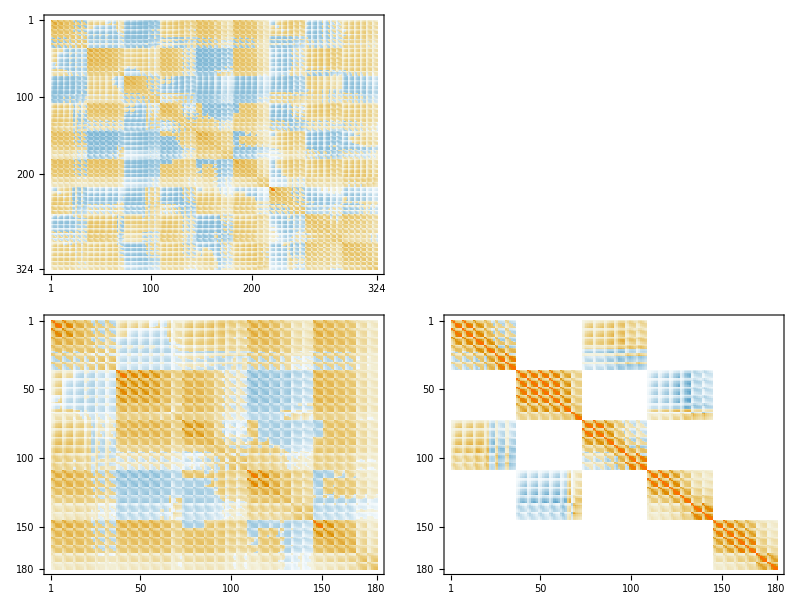

```mathematica
of=0;
DlikeS=Range[1+of,72,1];
DlikeD=Range[109+of,216,1];
DlikeRange=Join[DlikeS,DlikeD];
(*DlikeRange=Range[5,125,1]*)
If[(Length[DlikeRange]!=(Length[DevecGSp] DAdim)),Print["selected number of states ≠ Dim(D⊗a)  ",Length[DlikeRange],"≠",Length[DevecGSp] DAdim]];
DlikePartofH=FSHamBare[[1]][[1]][[DlikeRange,DlikeRange]];
DlikePartofN=FSNormBare[[1]][[1]][[DlikeRange,DlikeRange]];
orderedEVDr=Sort[Transpose[Eigensystem[{DlikePartofH,DlikePartofN}]],Re[#1[[1]]]<Re[#2[[1]]]&];
DevalGSr=orderedEVDr[[1]][[1]];
DevecGSr=orderedEVDr[[1]][[2]];
Print["Vector norm of GS (generalized EVP) = ",Norm[DevecGSr]];
Print["B(in reduced, D-like space) = ",Style[DevalGSr,Red]," MeV"];

DBasisDim=Length[DevecGSr];
Print["Deuteron-basis Dimension = ",DBasisDim];
Grid[{{MatrixPlot[FSHamBare[[1]][[1]],ImageSize->Large],MatrixPlot[FSNormBare[[1]][[1]],ImageSize->Large]},{MatrixPlot[DlikePartofH,ImageSize->Large],MatrixPlot[DlikePartofN,ImageSize->Large]}}]
```

for each of the states with the deuteron quantum numbers on the first two particles, there are a number of other which couple the third particle in appropriate ways *and* each vector’s radial dependence is expanded with a constant number of Gaussians. Hence the larger block size. In the example above, the S-wave cfg comprises two block each of side length 20=5 (particle1,2 widths) · 4(particle3 widths); the two blocks are ⊥ because they couple to a total spin 1/2 and 3/2 while being identical in their coordinate-space coupling structure.
c_1^(s)→1…4, c_2^(s)→5…8, …, c_10^(s)→1…40
c_11^(d)→61…64, c_12^(d)→65…68, …, c_25^(d)→117…120
A specific state Dais parametrized by selecting *one* index per block; a physically-inspired choice is to choose the largest index as that conventionally corresponds to the largest width, i.e., the broadest Gaussian and thereby a relatively large separation between the cm of particles 12 and the 3rd one.

we obtain all the other Da,a∈{1,2,...,4^(dim(D))}, in principle, by distributing the D’s expansion coefficients c_j appropriately in the vector cj; however, since 4^25 is quite a large number, we start with a random subset.

```mathematica
ciAs={};
UeCo=DevecGSp;
Do[
aI={};
bvn=1;
tmp=ConstantArray[0,FSbasisDim[[1]][[1]]];

Do[
lb=DAdim bv;
(* widths are ordered descending; hence, ub-1 selects a small one in order
"to keep the 3rd particle away from the deuteron" *)
aInd=lb+Na;(*RandomInteger[{lb,ub}];*)
AppendTo[aI,{aInd,UeCo[[bvn]]}];
bvn+=1;
,{bv,DbvIndices}];

Do[tmp[[m[[1]]]]=m[[2]];,{m,aI}];
AppendTo[ciAs,tmp];
,{Na,DAdim}];

Print[ciAs[[1]]//MatrixForm,ciAs[[2]]//MatrixForm]
```

(-0.00347769
0
0
0
0
0
-0.238772
0
0
0
0
0
-0.000692263
0
0
0
0
0
-0.000791676
0
0
0
0
0
-0.00021863
0
0
0
0
0
0.000125863
0
0
0
0
0
0.00459627
0
0
0
0
0
0.793524
0
0
0
0
0
-0.556291
0
0
0
0
0
0.000369395
0
0
0
0
0
-0.000360988
0
0
0
0
0
-0.0000338786
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0.040956
0
0
0
0
0
-0.00655577
0
0
0
0
0
0.00129027
0
0
0
0
0
-0.000019374
0
0
0
0
0
-0.000673838
0
0
0
0
0
-0.0013429
0
0
0
0
0
-0.00294749
0
0
0
0
0
0.00353169
0
0
0
0
0
0.0174485
0
0
0
0
0
-0.0000490166
0
0
0
0
0
0.00128852
0
0
0
0
0
-0.0000254388
0
0
0
0
0
0.00241981
0
0
0
0
0
-0.0381686
0
0
0
0
0
-0.0172417
0
0
0
0
0
-0.00125484
0
0
0
0
0
0.000730278
0
0
0
0
0
0.0000186298
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0)(0
-0.00347769
0
0
0
0
0
-0.238772
0
0
0
0
0
-0.000692263
0
0
0
0
0
-0.000791676
0
0
0
0
0
-0.00021863
0
0
0
0
0
0.000125863
0
0
0
0
0
0.00459627
0
0
0
0
0
0.793524
0
0
0
0
0
-0.556291
0
0
0
0
0
0.000369395
0
0
0
0
0
-0.000360988
0
0
0
0
0
-0.0000338786
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0.040956
0
0
0
0
0
-0.00655577
0
0
0
0
0
0.00129027
0
0
0
0
0
-0.000019374
0
0
0
0
0
-0.000673838
0
0
0
0
0
-0.0013429
0
0
0
0
0
-0.00294749
0
0
0
0
0
0.00353169
0
0
0
0
0
0.0174485
0
0
0
0
0
-0.0000490166
0
0
0
0
0
0.00128852
0
0
0
0
0
-0.0000254388
0
0
0
0
0
0.00241981
0
0
0
0
0
-0.0381686
0
0
0
0
0
-0.0172417
0
0
0
0
0
-0.00125484
0
0
0
0
0
0.000730278
0
0
0
0
0
0.0000186298
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0)

```mathematica
Select[ciAs[[1]],#!=0&]==UeCo
```

True

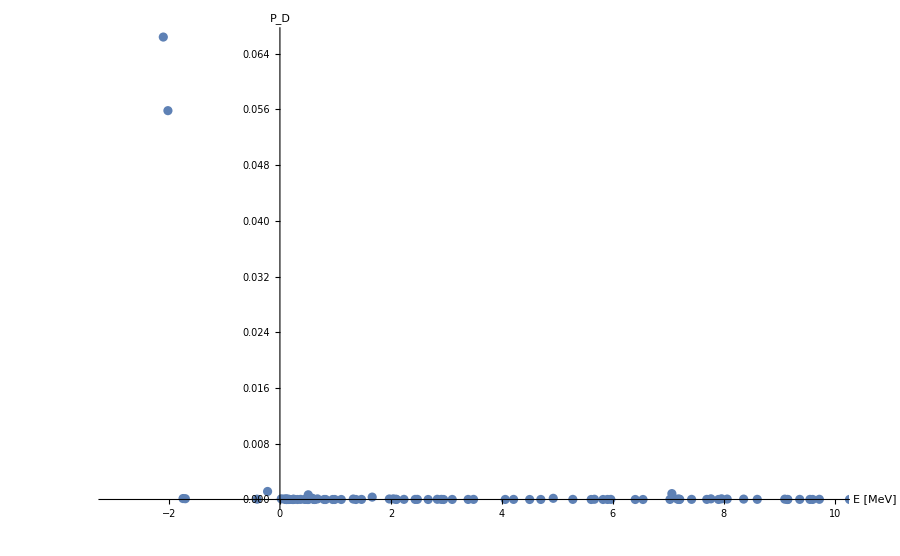

```mathematica
Jf=1;Basf=1;
nij=FSNormBare[[Jf]][[Basf]];
nab=Table[ciAs[[a]].nij.ciAs[[b]],{a,DAdim},{b,DAdim}];
Tik=IdentityMatrix[Dimensions[fulltrafosαβInstab[[Jf]][[Basf]]]];(*fulltrafosαβInstab[[Jf]][[Basf]];*)
(*Print["TemplateBox[{\"Da\", \"Db\"},\"BraKet\"] = ",nab//MatrixForm,"     SuperscriptBox[TemplateBox[{\"Da\", \"Db\"},\"BraKet\"], RowBox[{\"-\", \"1\"}]] = ",Inverse[nab]//MatrixForm]*)
DaEn=Table[(ciAs[[a]].nij).(esysFSp[[Jf]][[Basf]][[eE]][[2]].Tik),{eE,FSbasisDim[[Jf]][[Basf]]},{a,DAdim}];
maxEindex=FSbasisDim[[Jf]][[Basf]];
DaNDb=Table[{esysFSp[[Jf]][[Basf]][[EE]][[1]],Total[Table[DaEn[[EE]][[a]] Inverse[nab][[a]][[b]] DaEn[[EE]][[b]],{a,DAdim},{b,DAdim}],2]},{EE,maxEindex}];
ListPlot[DaNDb,AxesLabel->{"E [MeV]","P_D"},ImageSize->ImgSize,PlotRange->{{-3,10},All}]
```

```mathematica
Jf=1;Basf=2;
nij=FSNormBare[[Jf]][[Basf]];
hij=FSHamBare[[Jf]][[Basf]];
aa=1;bb=1;
hab=ciAs[[aa]].hij.ciAs[[bb]]
nab=ciAs[[aa]].nij.ciAs[[bb]]
hab/nab
```

53.1004

0.981787

54.0855

“sanity” check:  what is ∑_(n=0)^(FS-dim) P_D(E^(n))=?
this is a treacherous sum as it brings us back to what reality P_D  is connected with.

```mathematica
Total[DaNDb[[All,2]]]
```

0.0827292

#### Read RHS ⟨α|O_Lm_L|n⟩

the calculation is parallel in n_k parts

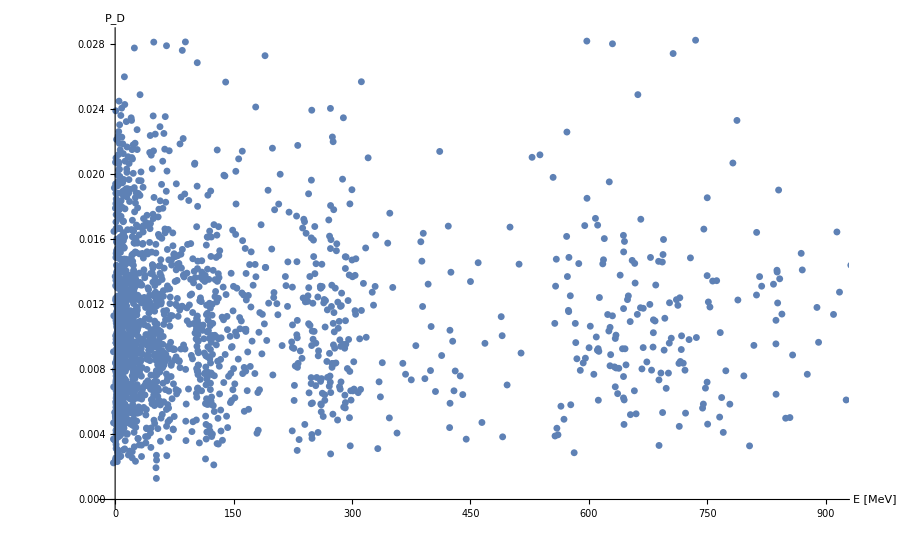
```mathematica
Show[-Graphics-,PlotRange->{{-3,5},Automatic}]
```